```mathematica
H={{1,1},{1,-1}}/Sqrt[2];
X={{0,1},{1,0}};
Z={{1,0},{0,-1}};
Y={{0,-I},{I,0}};
CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}; 
NOTC={{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}; 
XNOTC={{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}; 
%//MatrixForm
Phase[phi_,pauli_]:=MatrixExp[I phi * pauli]
Phase[Pi/8,Z]//MatrixForm
KroneckerProduct[X,H];
%//MatrixForm
%[[{1,2},{2,3}]]//MatrixForm
NToffoli=IdentityMatrix[8];
NToffoli[[{1,2},{1,2}]]=X;
RevNToffoli=IdentityMatrix[8];
RevNToffoli[[{1,5},{1,5}]]=X;
```

(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

(ⅇ^((ⅈ π)/8) | 0
0 | ⅇ^(-(ⅈ π)/8))

(0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0)

(0 | 1/(√2)
0 | 1/(√2))

(0.0322461+0.412112 ⅈ | 0.0529849-0.285403 ⅈ | 0.372343+0.229762 ⅈ | 0.436976-0.0737238 ⅈ
-0.429694-0.164529 ⅈ | 0.408955+0.362044 ⅈ | 0.295702-0.123792 ⅈ | 0.139665-0.27983 ⅈ
0.114277+0.270315 ⅈ | -0.1875-0.17891 ⅈ | -0.196491+0.246559 ⅈ | -0.174044+0.0800815 ⅈ
0.16847+0.0539097 ⅈ | -0.220247+0.0417612 ⅈ | -0.174044-0.275888 ⅈ | 0.00514951-0.411187 ⅈ)

{0.995078,0.936608,0.350378,0.0990974}

8.88178×10^-16+28.0314 x-1.77636×10^-14 x^2-266.764 x^3+5.68434×10^-14 x^4+477.465 x^5-2.84217×10^-14 x^6-238.732 x^7

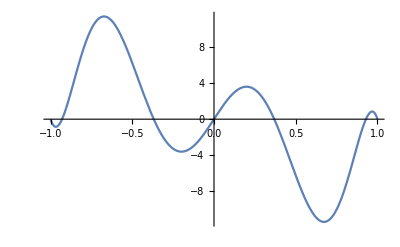

8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

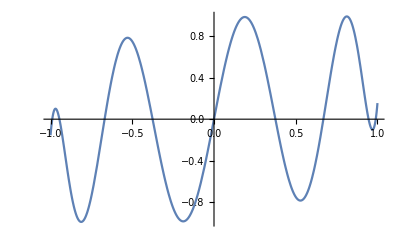

```mathematica
U=KroneckerProduct[NOTC,X].
KroneckerProduct[Phase[Pi/4,Y],Phase[Pi/8,Z],Phase[Pi/16,X]].
KroneckerProduct[Z,NOTC].
KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Y]].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/4,X],Phase[Pi/8,Y],Phase[Pi/16,Z]].KroneckerProduct[X,NOTC].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Z]];
A=U[[Range[1,4],Range[1,4]]]//N;
A//MatrixForm
SingularValueList[A]
poly1=InterpolatingPolynomial[{#,1/(4#)}&/@Join[%,-%],x]//Simplify
Plot[poly1,{x,-1,1}]
poly=InterpolatingPolynomial[Join[{#,1/(14#)}&/@Join[%%%,-%%%],{{-0.7,-0.3},{0.7,0.3}}],x]//Simplify//Chop
Plot[poly,{x,-1,1}]
```

1-66.6411 x^2+1527.13 x^4-13666.8 x^6+62278.5 x^8-161079. x^10+246379. x^12-220744. x^14+107124. x^16-21751.1 x^18

147.483

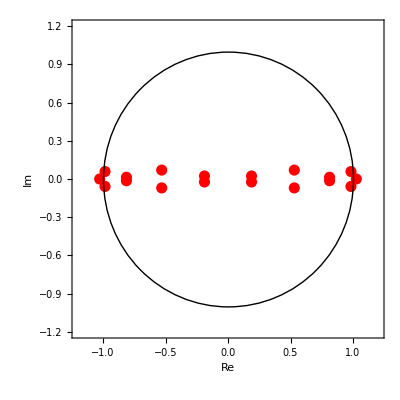

1.026608940584278

0.23221954458566 x+1.026608940584278 ⅈ √(1-x^2)

{-0.0359926035031957+1.001139800887216 x^2+0.047758778465269 ⅈ x √(1-x^2),-0.286141518198973+1.013561261037882 x^2+0.16524657296507 ⅈ x √(1-x^2),-0.660346309561149+1.00112326389231 x^2+0.04741085852833 ⅈ x √(1-x^2),-0.971154923209635+1.09173331742805 x^2+0.43804296179994 ⅈ x √(1-x^2)}

2.65346 x-53.9369 x^3+223.971 x^5-326.267 x^7+154.568 x^9+(0.+1. ⅈ) √(1-x^2)-(0.+36.341 ⅈ) x^2 √(1-x^2)+(0.+210.011 ⅈ) x^4 √(1-x^2)-(0.+379.942 ⅈ) x^6 √(1-x^2)+(0.+213.641 ⅈ) x^8 √(1-x^2)

1.+2.65346 x-36.341 x^2-53.9369 x^3+210.011 x^4+223.971 x^5-379.942 x^6-326.267 x^7+213.641 x^8+154.568 x^9

0.+2.65346 x-53.9369 x^3+223.971 x^5-326.267 x^7+154.568 x^9

1.-36.341 x^2+210.011 x^4-379.942 x^6+213.641 x^8

1.+1.59872×10^-14 x^2-5.68434×10^-13 x^4-3.63798×10^-12 x^8-2.91038×10^-11 x^10+1.16415×10^-10 x^12-8.73115×10^-11 x^14+4.36557×10^-11 x^16-7.27596×10^-12 x^18

```mathematica
1-poly^2//Expand
(*Plot[%,{x,-1,1}]*)
(*x/.{Roots[1-poly^2==0,x,WorkingPrecision->60]//ToRules}*)
K=Sqrt[-Coefficient[%,x^18]]
x/.NSolve[1-poly^2==0,x,WorkingPrecision->16];
p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]
s=%%%[[18]]
Rp=Sqrt[s^2-1]x+I s Sqrt[1-x^2]
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@{%%%%%[[11]],%%%%%[[13]],%%%%%[[15]],%%%%%[[17]]})
Wp=K*Rp*Qp[[1]]*Qp[[2]]*Qp[[3]]*Qp[[4]]//Expand//Simplify
%/.{Sqrt[1-x^2]->-I}//Chop
Bp=(%-(%/.x->-x))/2//Simplify
Cp=(%%+(%%/.x->-x))/2//Simplify
Bp^2+(1-x^2)Cp^2+poly^2//Expand
```

```mathematica
Mat={{poly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,poly-I Bp}}
ph9=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph8=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph7=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph6=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph5=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph4=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph3=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph2=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph1=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(%[[1,2]]/.{Sqrt[1-x^2]->-I})//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph0=%[[1,1]]
(R={{x,Sqrt[1-x^2]},{Sqrt[1-x^2],-x}})//MatrixForm
phs={I*ph0*ph9,ph1,ph2,ph3,ph4,ph5,ph6,ph7,ph8}/I//Arg;
NewMat=Dot@@Table[Phase[phs[[i]],Z].R,{i,1,Length[phs]}]//Expand//Simplify;
NewMat[[1,1]]-poly-I Bp//Expand//CoefficientList[#,x]&//Norm[#,1]&
```

{{8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9+ⅈ (0.+2.65346 x-53.9369 x^3+223.971 x^5-326.267 x^7+154.568 x^9),√(1-x^2) (1.-36.341 x^2+210.011 x^4-379.942 x^6+213.641 x^8)},{-√(1-x^2) (1.-36.341 x^2+210.011 x^4-379.942 x^6+213.641 x^8),8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9-ⅈ (0.+2.65346 x-53.9369 x^3+223.971 x^5-326.267 x^7+154.568 x^9)}}

0.371823+0.928304 ⅈ

0.943484+0.331418 ⅈ

0.993583+0.113104 ⅈ

0.997673+0.0681745 ⅈ

0.976776-0.214265 ⅈ

0.976776-0.214265 ⅈ

0.997673+0.0681745 ⅈ

0.993583+0.113104 ⅈ

0.943484+0.331418 ⅈ

0.928304-0.371823 ⅈ

(x | √(1-x^2)
√(1-x^2) | -x)

4.61636×10^-12

```mathematica
HHL=Dot@@Table[KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[Phase[phs[[i]],Z],IdentityMatrix[8]].KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[IdentityMatrix[2],MatrixPower[U//N,(-1)^i]],{i,1,Length[phs]}];
HHL=KroneckerProduct[H,IdentityMatrix[8]].HHL.KroneckerProduct[H,IdentityMatrix[8]];
HHL[[1;;4,1;;4]];
%//MatrixForm
(%%*14-AInv)//Norm
```

(0.123302+0.0612786 ⅈ | -0.152829-0.0961579 ⅈ | -0.285155-0.164685 ⅈ | 0.126288-0.179026 ⅈ
0.145875+0.0869695 ⅈ | -0.105248-0.107894 ⅈ | -0.321182-0.0670514 ⅈ | 0.0644302-0.211255 ⅈ
-0.0438065-0.122915 ⅈ | 0.101795+0.0066714 ⅈ | 0.141445-0.026424 ⅈ | -0.14997+0.0860774 ⅈ
0.092266+0.107257 ⅈ | -0.0831759+0.0223294 ⅈ | -0.18533-0.00368527 ⅈ | 0.126955-0.0112672 ⅈ)

6.05777×10^-13

```mathematica
AInv=Inverse[A]
NA=Table[(Abs[#^2]&)/@(AInv.IdentityMatrix[4][[k]]//Normalize),{k,1,4}]//Transpose;
NA//MatrixForm
BarChart3D[(*Reverse/@*)NA//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

{{1.72623+0.8579 ⅈ,-2.13961-1.34621 ⅈ,-3.99217-2.30559 ⅈ,1.76803-2.50636 ⅈ},{2.04225+1.21757 ⅈ,-1.47347-1.51052 ⅈ,-4.49654-0.938719 ⅈ,0.902023-2.95757 ⅈ},{-0.613291-1.72081 ⅈ,1.42513+0.0933997 ⅈ,1.98023-0.369936 ⅈ,-2.09958+1.20508 ⅈ},{1.29172+1.5016 ⅈ,-1.16446+0.312612 ⅈ,-2.59462-0.0515938 ⅈ,1.77737-0.157741 ⅈ}}

(0.223445 | 0.445733 | 0.399901 | 0.335836
0.339949 | 0.310592 | 0.39702 | 0.3413
0.200683 | 0.142276 | 0.0763586 | 0.209205
0.235923 | 0.101399 | 0.12672 | 0.113659)

-Graphics3D-

```mathematica
AInv//Round[#,0.1]&//MatrixForm
BarChart3D[(*Reverse/@*)AInv//Transpose//Abs//#^1&,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

(1.7+0.9 ⅈ | -2.1-1.3 ⅈ | -4.-2.3 ⅈ | 1.8-2.5 ⅈ
2.+1.2 ⅈ | -1.5-1.5 ⅈ | -4.5-0.9 ⅈ | 0.9-3. ⅈ
-0.6-1.7 ⅈ | 1.4+0.1 ⅈ | 2.-0.4 ⅈ | -2.1+1.2 ⅈ
1.3+1.5 ⅈ | -1.2+0.3 ⅈ | -2.6-0.1 ⅈ | 1.8-0.2 ⅈ)

-Graphics3D-